## Kramers-Krönig Hilbert transform

#### Definition: “f(x)=(-2/Pi)PV Int[x*g[y]/(y^2-x^2)]dy”;

Define the KKT as a function of analytic integration on the region 0 to 2π:

#### Note - this is the imaginary to real transform!!!! not the real to imaginary

```mathematica
analyticHT[fun_,y_,upperBound_]:=Integrate[((-2y)/Pi)*fun[x]/(x^2-y^2),{x,0,upperBound},PrincipalValue->True]//N
```

Define a numerical integration version for comparison :

```mathematica
numericalHT[fun_,y_,upperBound_,singularPointRad_,maxRecursions_,workingPrec_]:=NIntegrate[((-2y)/Pi)*fun[x]/(x^2-y^2),{x,0,upperBound},Method->{"PrincipalValue","SingularPointIntegrationRadius"->singularPointRad},MaxRecursion->maxRecursions,Exclusions->{((x^2)-(y^2))==0},WorkingPrecision->workingPrec]//N
```

#### Test on a simple function with known KKT, eg, cosine function:;

Note major instability issues wrt working precision and max recursions

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb,NIntegrate::par,NIntegrate::zeroregion]
analyticHT[Cos,2,2Pi]
numericalHT[Cos,2,2Pi,10^-10,200,55]
```

0.835679

0.835679

#### Plot to check that the cosine function KKTs to the sine function

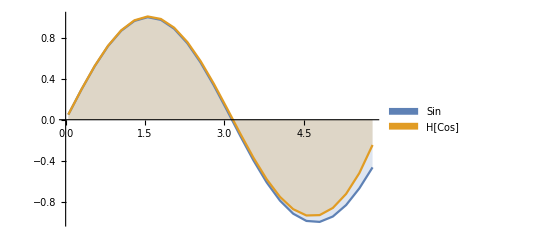

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb,NIntegrate::par,NIntegrate::zeroregion,NIntegrate::precw,NIntegrate::inumri,General::stop]
DiscretePlot[{Sin[y],analyticHT[Cos,y,2Pi]},{y,0.05,6,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

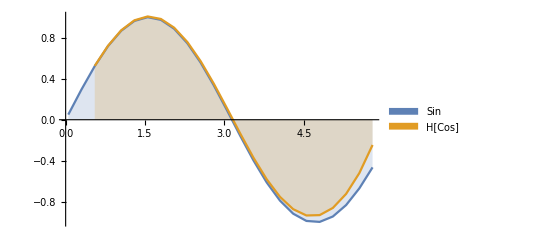

```mathematica
DiscretePlot[{Sin[y],numericalHT[Cos,y,2Pi,10^-10,200,55]},{y,0.05,6,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

#### Note - changing the integration upper bound to inifinty makes the Hilbert transform better at high values, but not so much at low values

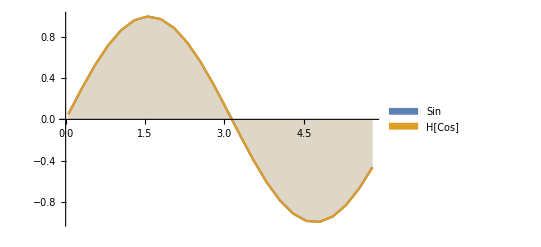

```mathematica
DiscretePlot[{Sin[y],analyticHT[Cos,y,Infinity]},{y,0.05,6,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

#### Check on a more realistic function, such as a cosine fitted on 20 points;

```mathematica
cosData=Table[{i*2Pi/20,Cos[i*2Pi/20]//N},{i,0,20}];
cosDataInter[x_]:=If[x>0&&x<2Pi,Interpolation[cosData][x],0]
```

```mathematica
Off[NIntegrate::eincr,General::stop]
```

```mathematica
sList=Table[Sin[i/2]//N,{i,1,12}]
hList=Table[numericalHT[cosDataInter,i/2,Infinity,10^-10,200,55],{i,1,12}]
```

{0.479426,0.841471,0.997495,0.909297,0.598472,0.14112,-0.350783,-0.756802,-0.97753,-0.958924,-0.70554,-0.279415}

{0.481589,0.845785,1.0042,0.918956,0.611931,0.159515,-0.325627,-0.721407,-0.926173,-0.879246,-0.566307,0.0481692}

#### Nice!

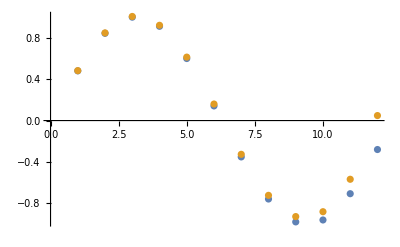

```mathematica
ListPlot[{sList,hList}]
```

## Realistic example

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/Band_life_broadened"];
phononSE=ReadList["se.all.Gamma.Gamma-X.X.X-W.W.W-K.K.K-Gamma.Gamma-L.L",{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}];
path={{0,0,0},{0,0,0},0.5({0,0,0}+{0,0.5,0.5}),{0,0.5,0.5},0.5({0,0.5,0.5}+{0.25,0.75,0.5}),{0.25,0.75,0.5},0.5({0.25,0.75,0.5}+{3/8,3/4,3/8}),{3/8,3/4,3/8},0.5({3/8,3/4,3/8}+{0,0,0}),{0,0,0},0.5({0,0,0}+{1/2,1/2,1/2}),{1/2,1/2,1/2}}
pathNorm=Table[Norm[path[[i]]-path[[i-1]]],{i,2,12}]
pathD=Table[Total@Table[pathNorm[[i]],{i,1,j}],{j,1,11}]
pList=Table[Table[pathD[[j]],{i,1,201}],{j,1,11}];
gammaData=Table[Transpose[{Transpose[phononSE][[1]],pList[[j]],Transpose[phononSE][[j+1]]}],{j,1,10}];
```

{{0,0,0},{0,0,0},{0.,0.25,0.25},{0,0.5,0.5},{0.125,0.625,0.5},{0.25,0.75,0.5},{0.3125,0.75,0.4375},{3/8,3/4,3/8},{0.1875,0.375,0.1875},{0,0,0},{0.25,0.25,0.25},{1/2,1/2,1/2}}

{0,0.353553,0.353553,0.176777,0.176777,0.0883883,0.0883883,0.459279,0.459279,0.433013,0.433013}

{0,0.353553,0.707107,0.883883,1.06066,1.14905,1.23744,1.69672,2.156,2.58901,3.02202}

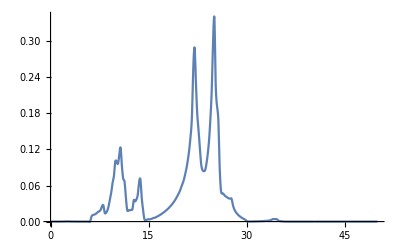

```mathematica
im[x_]:=If[0≤ x≤Transpose[gammaData[[1]]][[1]][[-1]],Interpolation[Transpose[{Transpose[gammaData[[1]]][[1]],Transpose[gammaData[[1]]][[3]]}]][x],0]
imP=Plot[im[x],{x,0,50},PlotRange->All]
```

```mathematica
imH=Table[{i,numericalHT[im,i,Infinity,10^-10,200,55]},{i,1,50}]
```

{{1,-0.00355475},{2,-0.00733053},{3,-0.0110127},{4,-0.0158459},{5,-0.0222134},{6,-0.0346481},{7,-0.0398061},{8,-0.0402596},{9,-0.0699139},{10,-0.0438722},{11,0.0398695},{12,0.0135435},{13,-0.00863692},{14,0.0407797},{15,-0.00224056},{16,-0.0208854},{17,-0.0357074},{18,-0.0497213},{19,-0.0651012},{20,-0.0835444},{21,-0.108189},{22,-0.0271872},{23,0.0652033},{24,-0.0280144},{25,0.0688155},{26,0.201573},{27,0.122854},{28,0.115809},{29,0.0937287},{30,0.0790431},{31,0.0654017},{32,0.0574594},{33,0.0514049},{34,0.0475461},{35,0.0475264},{36,0.0430914},{37,0.0399928},{38,0.0375675},{39,0.0355116},{40,0.0337229},{41,0.0321428},{42,0.0307317},{43,0.0294607},{44,0.0283079},{45,0.027256},{46,0.0262912},{47,0.0254022},{48,0.0245797},{49,0.023816},{50,0.0231045}}

InterpolatingFunction::dmval: Input value {0.00102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

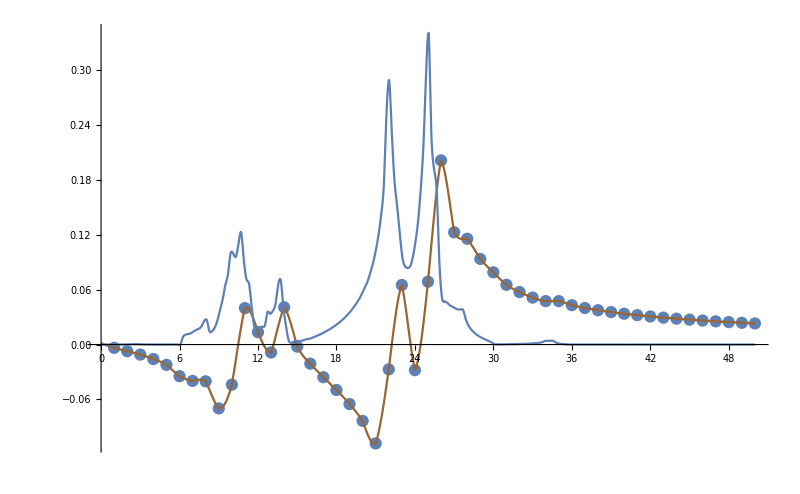

```mathematica
Show[{ListPlot[imH],Plot[Interpolation[imH][x],{x,0,50},PlotStyle->Brown],imP},PlotRange->All,ImageSize->800]
```

## BREAK

```mathematica
analyticHTmod[fun_,y_,upperBound_,lowerBound_]:=Integrate[((-2x)/Pi)*fun[x]/(x^2-y^2),{x,lowerBound,upperBound},PrincipalValue->True,Assumptions->{0≤x≤2Pi}]//N
```

```mathematica
analyticHTmod[cosDataInter,2,Infinity,0]
```

3.58433

```mathematica
Sin[2]//N
```

0.909297

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0503097}. NIntegrate obtained -4.97953 and 3.63769 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.299897025714088}. NIntegrate obtained 0.540555 and 1.42593 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.550387}. NIntegrate obtained 81.4825 and 81.7473 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

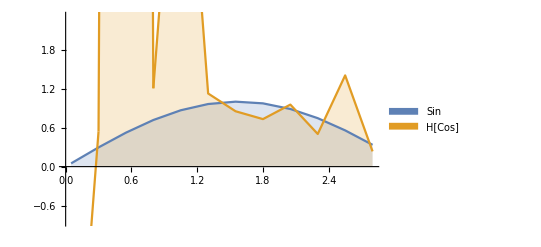

```mathematica
DiscretePlot[{Sin[y],analyticHTmod[cosDataInter,y,Infinity,-Infinity]},{y,0.05,3,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

```mathematica
DiscretePlot[analyticHT[Cos,y,Infinity],{y,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb]
```

{{0,1.},{π/10,0.951057},{π/5,0.809017},{(3 π)/10,0.587785},{(2 π)/5,0.309017},{π/2,0.},{(3 π)/5,-0.309017},{(7 π)/10,-0.587785},{(4 π)/5,-0.809017},{(9 π)/10,-0.951057},{π,-1.},{(11 π)/10,-0.951057},{(6 π)/5,-0.809017},{(13 π)/10,-0.587785},{(7 π)/5,-0.309017},{(3 π)/2,0.},{(8 π)/5,0.309017},{(17 π)/10,0.587785},{(9 π)/5,0.809017},{(19 π)/10,0.951057},{2 π,1.}}

```mathematica
cosDataInter[x_]:=If[x>0&&x<2Pi,Interpolation[cosData][x],0]
```

```mathematica
cos[x_]:=If[x>0&&x<2Pi,Interpolation[cosData][x],0]
```

```mathematica
"Assumptions→x>0&&y>0&&x∈Reals&&y∈Reals"
```

-0.817277

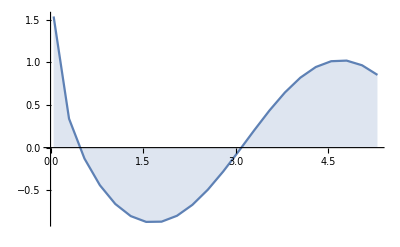

```mathematica
analyticHT[fun_,y_,upperBound_]:=Integrate[((2x)/Pi)*fun[x]/(x^2-y^2),{x,0,upperBound},PrincipalValue->True]//N
```

-0.835679

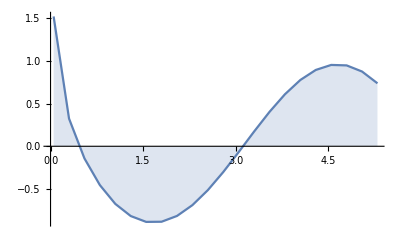

```mathematica
analyticHT[Cos,2,2Pi]
DiscretePlot[analyticHT[Cos,y,2Pi],{y,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

```mathematica
numericalHT[Cos,0.00000000000005,200,2Pi,60,2]
```

-0.839884444218854517959522738940957026144392959514571851922216

NIntegrate::precw: The precision of the argument function ((2 x Cos[x])/(π (-0.0025+x^2))) is less than WorkingPrecision (60.).

NIntegrate::precw: The precision of the argument function ((2 x Cos[x])/(π (-0.09+x^2))) is less than WorkingPrecision (60.).

NIntegrate::precw: The precision of the argument function ((2 x Cos[x])/(π (-0.3025+x^2))) is less than WorkingPrecision (60.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.55000000000000009741311699936857080835885489936551498216447,1.55000000000000009741311699936857080835885489936551498216448}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.80000000000000005921189464667501451535800350680451609659629,1.80000000000000005921189464667501451535800350680451609659629}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{2.04999999999999992201360217267192933563800817257642179958229,2.04999999999999992201360217267192933563800817257642179958229}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

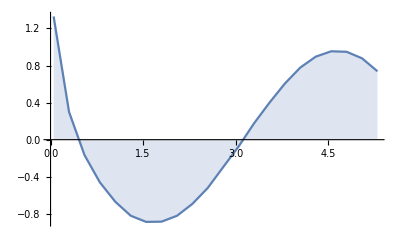

```mathematica
DiscretePlot[numericalHT[Cos,10^-10,200,2Pi,60,y],{y,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

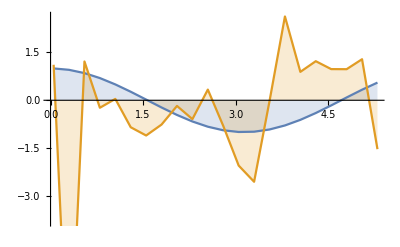

```mathematica
DiscretePlot[{cosDataInter[w],realCosHTnumerical[w]},{w,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

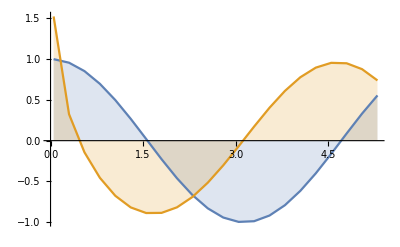

```mathematica
DiscretePlot[{cosDataInter[w],realCosHTanalyticInf2[w]},{w,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

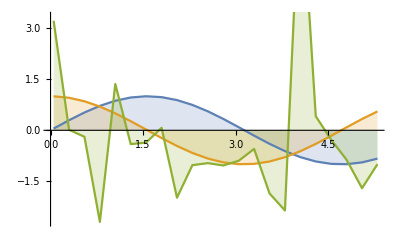

```mathematica
DiscretePlot[{Sin[w],cosDataInter[w],realCosHT[w]},{w,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

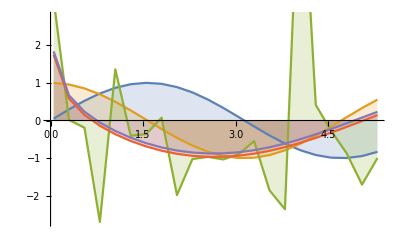

```mathematica
DiscretePlot[{Sin[w],cosDataInter[w],realCosHT[w],realCosHTanalytic[w],realCosHTanalyticInf[w]},{w,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

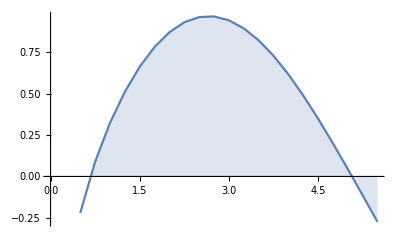

```mathematica
DiscretePlot[cosDataHT[w],{w,0.5,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

```mathematica
realCosHTanalyticInf
```

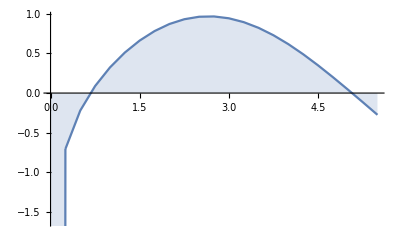

```mathematica
DiscretePlot[realCosHTanalytic[w],{w,0,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

InterpolatingFunction[{{0., 5.57932}}, <>]

NIntegrate::inumri: The integrand ((2.-a) «1»)/(-4.+(2.-a)^2)+((2.+a) «1»)/(-4.+(2.+a)^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,4.19552×10^-19}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{0.,4.1955189760564852530983259149912375675768374500918128186539480725×10^-19}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

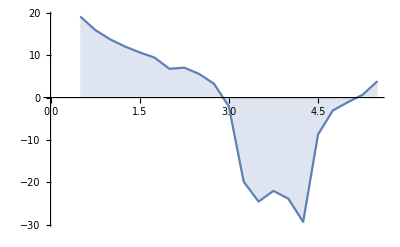

```mathematica
{epsilon1,w}=ToExpression@Import["http://pastebin.com/raw.php?i=Z08GwMa8"];
f=Interpolation[Transpose[{Flatten[w],Flatten[epsilon1]}]]
epsilon2[w_]:=epsilon2[w]=2/Pi NIntegrate[a f[a]/(a^2-w^2),{a,0,5.5793},Method->"PrincipalValue",Exclusions->{(a^2-w^2)==0}]//Quiet
DiscretePlot[epsilon2[w],{w,0.5,5.5,.25},AxesOrigin->{0,0},Joined->True]
```

```mathematica
analyticHT[cos,2,2Pi]
DiscretePlot[analyticHT[cos,y,2Pi],{y,0.05,5.5,.25},AxesOrigin->{0,0},Joined->True]
```